# Continuity of roots

```mathematica
x0=1+ⅈ;
x1=1-ⅈ;
x2=1+0.8 ⅈ;

f[x_]:=(x-x0)(x-x1)(x-x2)
γ[t_,ϵ_,p_]:=p+ϵ ⅇ^(2π ⅈ t)
```

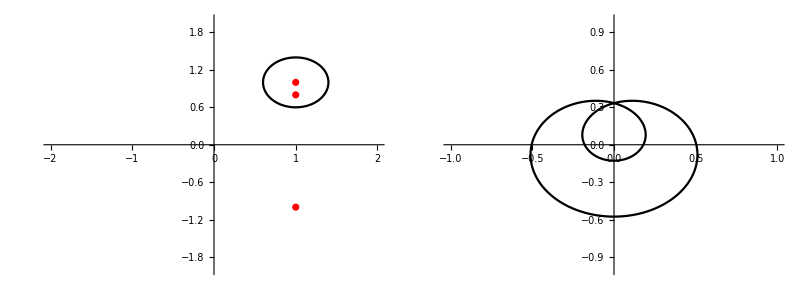

```mathematica
Grid[{{
Show[
ListPlot[ReIm[{x0,x1,x2}],PlotStyle->Red,PlotRange->{{-2,2},{-2,2}},AspectRatio->Automatic],
ParametricPlot[ReIm[γ[t,0.4,x0]],{t,0,1},PlotStyle->Black],
ImageSize->400
],
ParametricPlot[ReIm[f[γ[t,0.4,x0]]],{t,0,1},PlotStyle->Black,PlotRange->{{-1,1},{-1,1}},ImageSize->400]}}]
```

```mathematica
Manipulate[
Grid[{{
Show[
ListPlot[ReIm[{x0,x1,x2}],PlotStyle->Red,PlotRange->{{-2,2},{-2,2}},AspectRatio->Automatic],
ParametricPlot[ReIm[γ[t,ϵ,x0]],{t,0,1},PlotStyle->Black],
ImageSize->400
],
ParametricPlot[ReIm[f[γ[t,ϵ,x0]]],{t,0,1},PlotStyle->Black,ImageSize->400]}}]
,{{ϵ,0.4},0,0.5}]
```

```mathematica
Manipulate[
Grid[{{
Show[
ListPlot[ReIm[{x0,x1,x2}],PlotStyle->Red,PlotRange->{{-2,2},{-2,2}},AspectRatio->Automatic],
ParametricPlot[ReIm[γ[t,ϵ,0]],{t,0,1},PlotStyle->Black],
ImageSize->400
],
ParametricPlot[ReIm[f[γ[t,ϵ,0]]],{t,0,1},PlotStyle->Black,ImageSize->400]}}]
,{{ϵ,0.4},0,0.5}]
```